```mathematica
Ln1=4;
Ln2=1;
c=1;
```

P(l1<L1, l2< L2)

```mathematica
P1[l1_,l2_,c_,γ_]:=((l1+l2+c-1)!)/((c-1)!l1!l2!)*(1/(2+γ))^(l1+l2)(γ/(2+γ))^c
```

P(l1<L1,l2=L2)

```mathematica
P2[l1_,L2_,c_,γ_]:=((l1+c-1)!)/(l1!(c-1)!)*γ^c/(γ+1)^(l1+c)-Sum[((l1+l2+c-1)!)/((c-1)!l1!l2!)*γ^c/(γ+2)^(l1+l2+c),{l2,0,L2-1}]
```

P(l1=L1,l2=L2). First term is all structures l1=(0-L1-1), l2=(0:L2). Second term is l1=L1, l2=L2-1. Note that L1 cannot be less than 1.

```mathematica
P3[L1_,L2_,c_,γ_]:=1-Sum[Sum[P1[l1,l2,c,γ],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ],{l2,0,L2-1}]
```

Note that also L2 Cannot be less than 1.

Entropy

```mathematica
En[L1_,L2_,c_,γ_]:=-Sum[Sum[P1[l1,l2,c,γ]*Log[P1[l1,l2,c,γ]],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ]*Log[P2[l1,L2,c,γ]],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ]*Log[P2[l2,L1,c,γ]],{l2,0,L2-1}]-P3[L1,L2,c,γ]*Log[P3[L1,L2,c,γ]]
```

For separate proteins, (one compartment!)

P(l1, l2<L1,L2)

```mathematica
P4[l1_,l2_,p_]:=(1-p)^2* p^(l1+l2)
```

P(l=L1,l2<L2)

```mathematica
P5[l1_,L2_,p_]:=(1-p)*p^(l1+L2)
```

P(l1,l2=L1,L2)

```mathematica
P6[L1_,L2_,p_]:=p^(L1+L2)
```

KL Divergence

```mathematica
KL[L1_,L2_,γ_]:=Sum[Sum[P1[l1,l2,c,γ]*Log[P1[l1,l2,c,γ]/P4[l1,l2,1/(1+γ)]],{l1,0,L1-1}],{l2,0,L2-1}]+Sum[P2[l1,L2,c,γ]*Log[P2[l1,L2,c,γ]/P5[l1,L2,1/(1+γ)]],{l1,0,L1-1}]+Sum[P2[l2,L1,c,γ]*Log[P2[l2,L1,c,γ]/P5[l2,L1,1/(1+γ)]],{l2,0,L2-1}]+P3[L1,L2,c,γ]*Log[P3[L1,L2,c,γ]/P6[L1,L2,1/(1+γ)]]
```

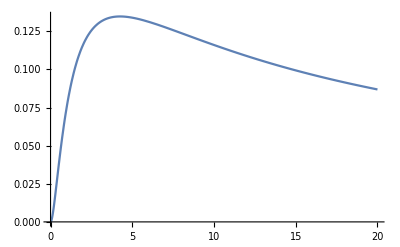

```mathematica
Plot[KL[4,1,1/τ],{τ,0,20}]
```